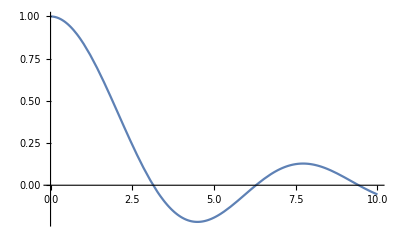

```mathematica
u[x_]:= If[x ≠ 0, (Sin[x])/x, 1]
Plot[u[x], {x, 0, 10}]
```

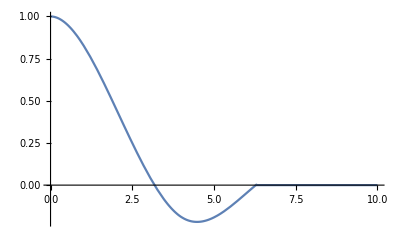

```mathematica
u[x_]:=If[x≤2, 0.032766*x^3-0.20191*x^2+0.000070388*x+1.0, 
             If[x≤4, 0.025765*x^3-0.15989*x^2-0.084017*x+1.0561, 
           If[x≤6.3, -0.025303*x^3+0.45309*x^2-2.5365*x+4.3269,0]]]
Plot[u[x], {x, 0, 10}]
```

```mathematica
f[x_]:=D[Sin[x]/x,x]
```

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[(Sin[x])/(x),x]
```

Cos[x]/x-Sin[x]/x^2

```mathematica
f[x_]:= Cos[x]/x-Sin[x]/x^2
```

```mathematica
f[0.001]
```

-0.000333333

```mathematica
f[20.001]
```

0.0180743

```mathematica
f[7.001]
```

0.0941716

```mathematica
f[6.001]
```

0.16778